```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
h[n_,ρ_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar,tw=ρ ts},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
(* periodic bc *)
PrependTo[tblw,{1,1+F0}->tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* overlap matrix; we assume that the overlaps Subscript[γ, s], Subscript[γ, w] are distributed as the couplings and that Subscript[γ, w]/Subscript[γ, s] = Subscript[t, w]/Subscript[t, s] *)
ov[n_,ρ_,γs_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar,γw=ρ γs,diag},
tblw=Table[{i,i+F0}->γw,{i,2,F1}];
tbls=Table[{i,i+F1}->γs,{i,1,F0}];
(* periodic bc *)
PrependTo[tblw,{1,1+F0}->γw];
(* diagonal terms *)
diag=Table[{i,i}->1/2,{i,F2}];
ar=SparseArray[diag,{F2,F2}]+SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

How does the overlap between orbitals deform/asymmetrize the spectrum?

```mathematica
n=12;
ρ=1./2.;
ts=1.;
γs=0.1*ts;
(* deformed spectrum *)
sp=Sort@Eigenvalues[{h[n,ρ,ts],ov[n,ρ,γs]}];
(* nondeformed spectrum *)
sp0=Sort@Eigenvalues[h[n,ρ,ts]];
```

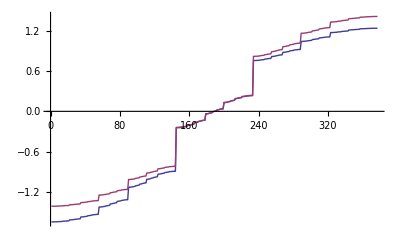

```mathematica
ListPlot[{sp,sp0},Joined->True]
```

Does enlarging the levels mix them?

```mathematica
Clear[η,ldos,ldos0]
n=9;
ρ=1./5.;
ts=1.;
γs=0.01*ts;
{val,vec}=Eigensystem[{h[n,ρ,ts],ov[n,ρ,γs]}];
{val0,vec0}=Eigensystem[h[n,ρ,ts]];
o=Ordering[val];
val=val[[o]];
vec=vec[[o]];
wf=vec;
o=Ordering[val0];
val0=val0[[o]];
vec0=vec0[[o]];
wf0=vec0;
(* G0[ω,η][[i]]: Green function Subscript[G, 0](i,i;ω) *)
int=Abs[wf]^2;
int0=Abs[wf0]^2;
G0[ω_,η_]:=Total[int/(ω+I η-val)];
(* local density of states at site i: -1/π Im Subscript[G, 0](i,i;ω) *)
ldos[ω_,η_]:=1/π Total[(int η)/((ω-val)^2+η^2)];
ldos0[ω_,η_]:=1/π Total[(int0 η)/((ω-val0)^2+η^2)];
```

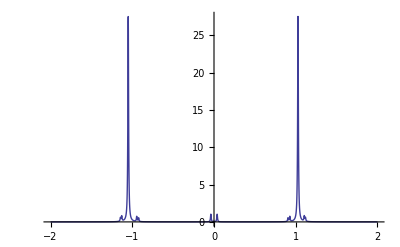

```mathematica
η=0.005*ts;
i=72;
Plot[{ldos[ω,η][[i]]},{ω,-2,2},PlotRange->All]
```

```mathematica
listom=val;
```

```mathematica
η=0.005*ts;
listldos=Abs[ldos[#,η]&/@listom];
```

```mathematica
ListContourPlot[listldos/Max[listldos],InterpolationOrder->0,PlotLegends->Automatic]
```

-Graphics-

What happens when t_s and t_w are randomized?

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hr[n_,ρ_,ts_,δ_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar,tw=ρ ts},
tblw=Table[{i,i+F0}->tw(1+δ RandomReal[{-1,1}]),{i,2,F1}];
tbls=Table[{i,i+F1}->ts(1+δ RandomReal[{-1,1}]),{i,1,F0}];
(* periodic bc *)
PrependTo[tblw,{1,1+F0}->tw(1+δ RandomReal[{-1,1}])];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
n=12;
ρ=1./2.;
ts=1.;
γs=0.1*ts;
δ=.01;
(* deformed spectrum *)
spr=Sort@Eigenvalues[hr[n,ρ,ts,δ]];
(* nondeformed spectrum *)
sp0=Sort@Eigenvalues[h[n,ρ,ts]];
```

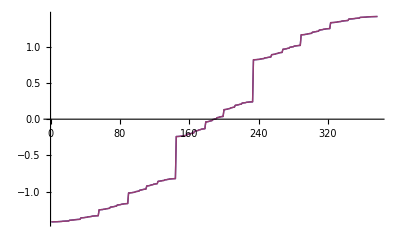

```mathematica
ListPlot[{spr,sp0},Joined->True]
```